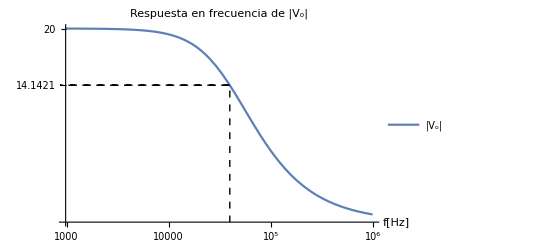

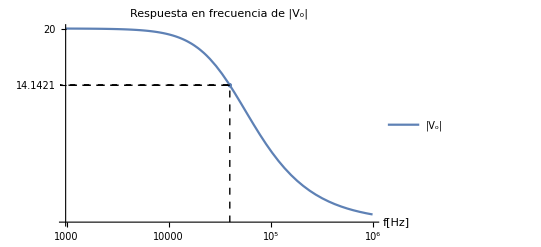

```mathematica
Clear["Global`*"]
vi = 20 ;
r = 2000;
c = 2000*10^-12;
zc = -ⅉ/(2*Pi*f*c);
vo[f_] = vi *(zc/(r+zc));
voabs[f_]=ComplexExpand[Abs[FullSimplify[vo[f]]]];
fo = f /. Solve[voabs[f]== 1/(√2)voabs[0],f][[2]]//N;
a = LogLinearPlot[{voabs[f]},{f,0,10^6},
Epilog->{Dashed, Line[{{Log[fo],voabs[fo]},{Log[1],voabs[fo]},{Log[fo],voabs[fo]},{Log[fo],0}}]},
Ticks->{Join[{fo},Table[10^i,{i,0,6}]],{voabs[fo]//N,20}},
PlotLabel->"Respuesta en frecuencia de |V_o|",
PlotLegends->{"|V_o|"},
AxesLabel->{"f[Hz]",None}]
b = ListLogLinearPlot[{{fo,voabs[fo]}},PlotStyle->PointSize[Large]];
Show[a,b]
```